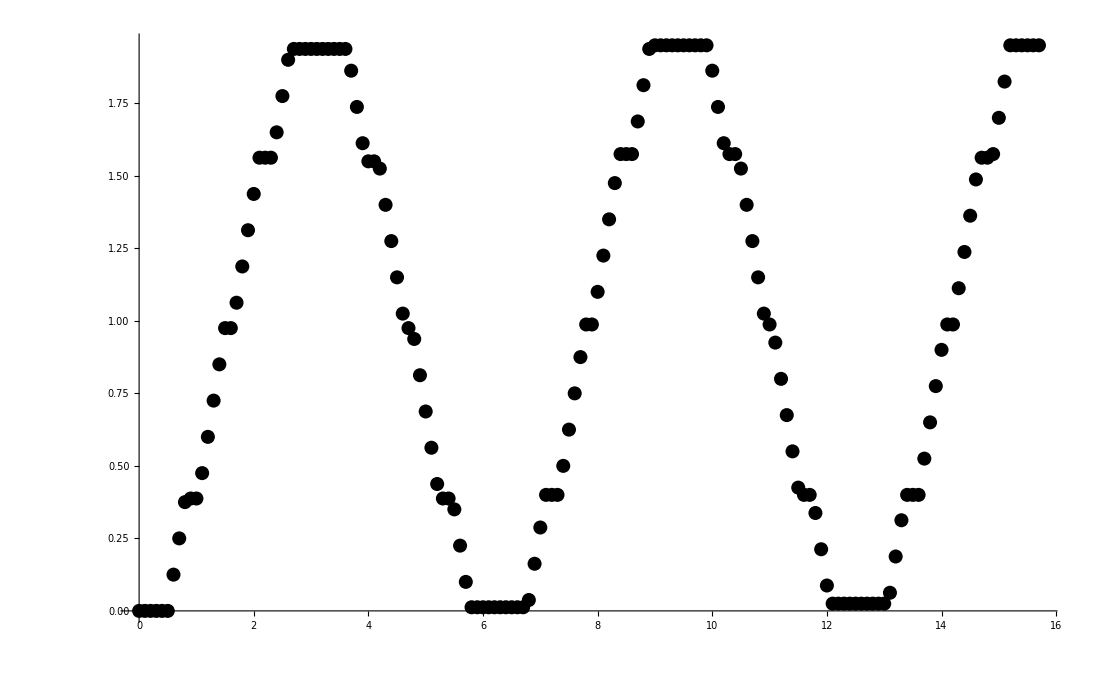

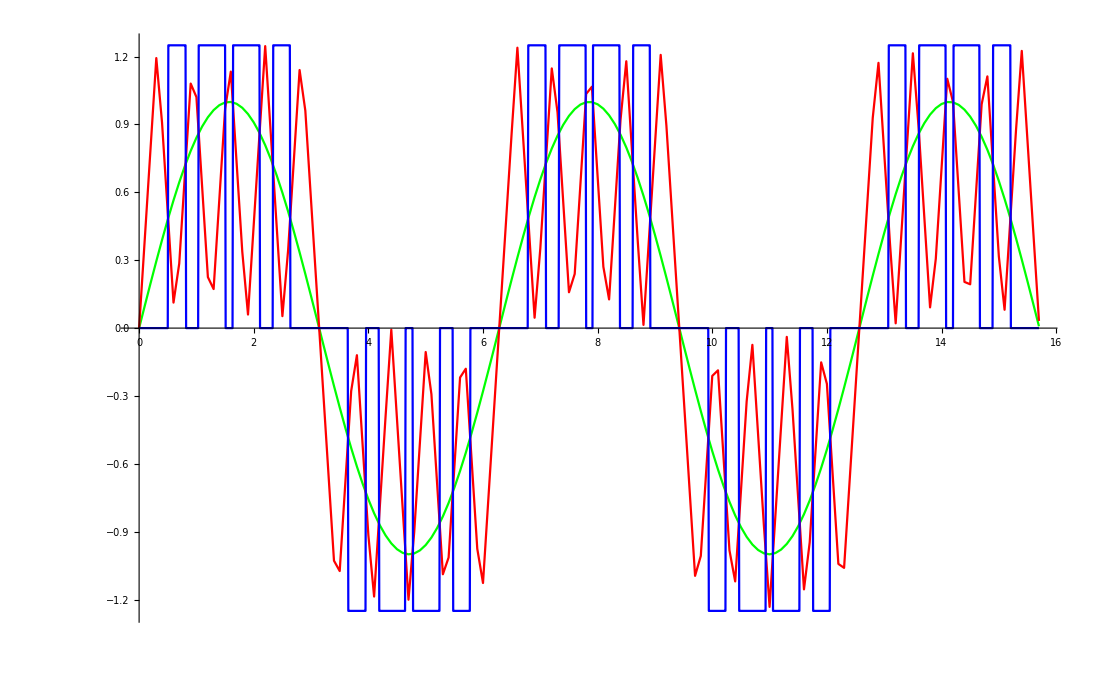

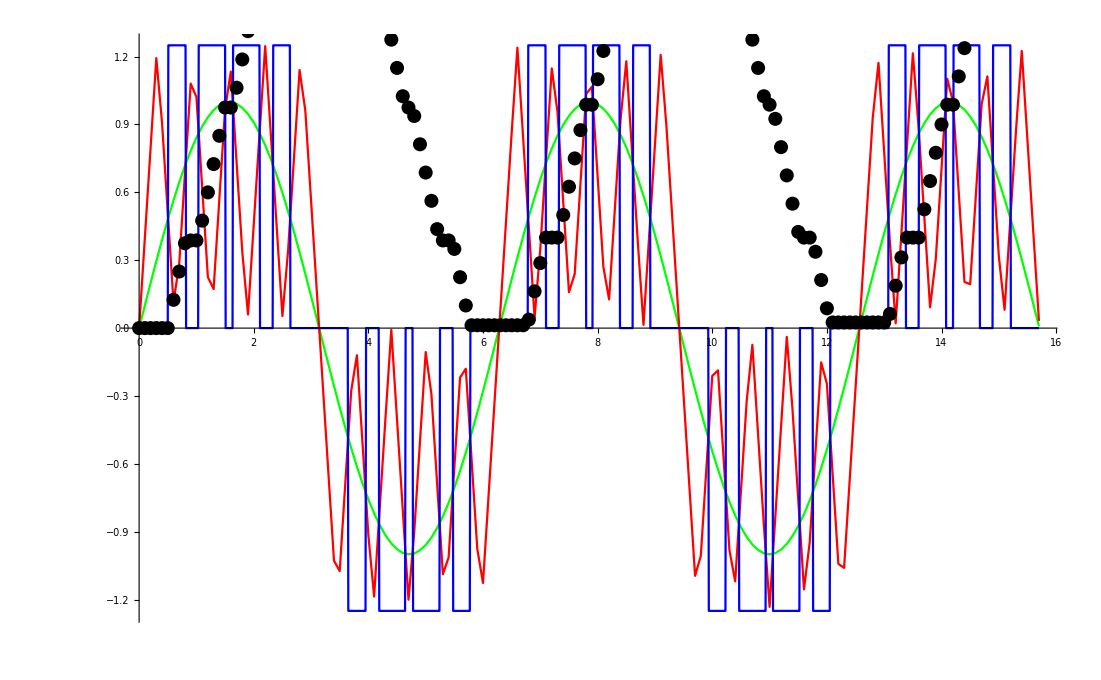

```mathematica
ClearAll;
DD=0.1;
NN=10;
SS1[x_]:=N[Sin[x],15];
SS2[x_]:=If[Sin[x]<0,-1,1];
TT1[x_,n_]:=N[2.5*Abs[Round[(n/2*x)/π]-((n/2*x)/π)],15];
TT3[x_,n_]:=TT1[x,n]*SS2[x]
TT4[x_,n_]:=If[Abs[SS1[x]]>TT1[x,n],1.25*SS2[x],0]
LS1[xx_,yy_,nn_]:=Table[{x,SS1[x]},{x,xx,yy,DD}];
LT3[xx_,yy_,nn_]:=Table[{x,TT3[x,nn]},{x,xx,yy,DD}];
LT4[xx_,yy_,nn_]:=Table[{x,TT4[x,nn]},{x,xx,yy,DD*0.1}];
AA1[xx_,nn_,dd_]:=Sum[TT4[yy,nn]*dd,{yy,0,xx,dd}];
LA1[xx_,yy_,nn_]:=Table[{x,AA1[x,nn,DD*0.1]},{x,xx,yy,DD}];
aaaa3=ListPlot[
{
LS1[0,5π,NN],
LT3[0,5π,NN],
LT4[0,5π,NN]
},PlotLegends->"Expressions",Joined->True,PlotStyle->{Green,Red,Blue}];
aaaa4=ListPlot[
{
LA1[0,5π,NN]
},PlotLegends->"Expressions",Joined->False,PlotStyle->{Black}];
Show[{aaaa4}]
Show[{aaaa3}]
Show[{aaaa3,aaaa4}]
```